ListPlot::prng: Value of option PlotRange -> {{All}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

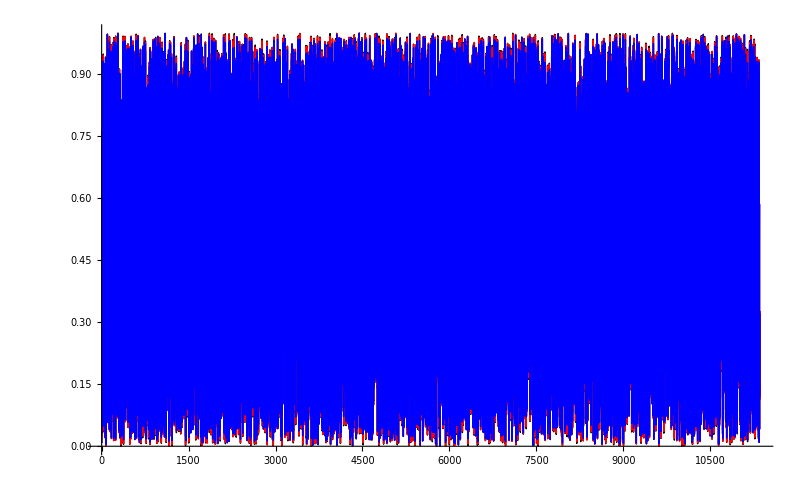

```mathematica
ListPlot[{signal,result,result2},PlotStyle-> {Black,Red,Blue},Joined->True,PlotRange->{{11302,11352}}]
```

```mathematica
Total[Abs[signal-result]]
Total[Abs[signal-result2]]
```

1120.43

1074.08

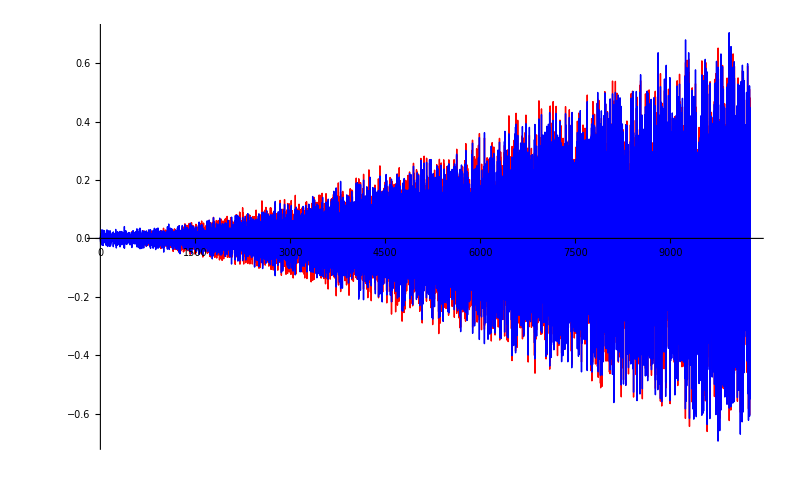

```mathematica
ListPlot[{signal-result,signal-result2},PlotStyle-> {Red,Blue},Joined->True,PlotRange->{All,All}]
```

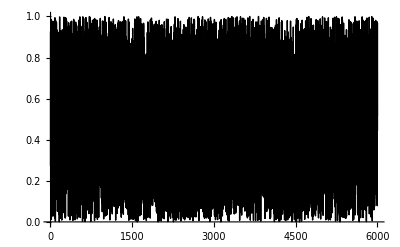

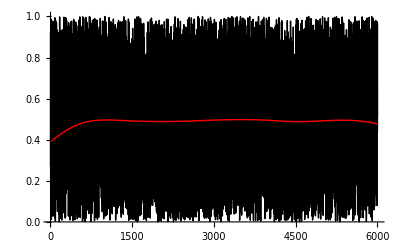

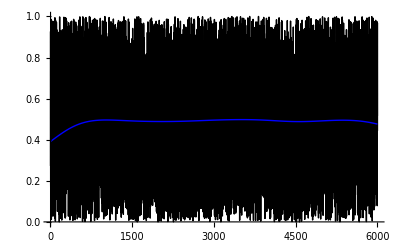

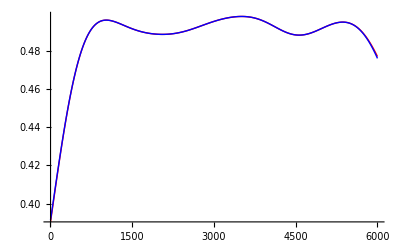

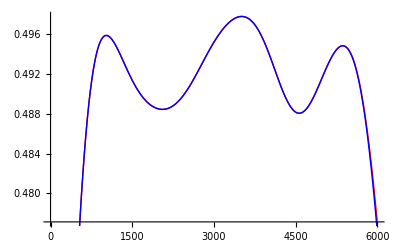

```mathematica
oracle=applylowpassfilter[signal,1000];

ListPlot[{signal},PlotStyle-> {Black},Joined->True,PlotRange->All]
ListPlot[{signal,result},PlotStyle-> {Black,Red},Joined->True,PlotRange->All]
ListPlot[{signal,oracle},PlotStyle-> {Black,Blue},Joined->True,PlotRange->All]
ListPlot[{result,oracle},PlotStyle-> {Red,Blue},Joined->True,PlotRange->All]
ListPlot[{result,oracle},PlotStyle-> {Red,Blue},Joined->True]
```